Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1.  In how many ways can a company assign 10 drivers to n buses, one driver to each bus and conversely?

The text answer of 10! ways to assign drivers eluded me for awhile. The 10! is an upper limit on the number of ways to scramble ten drivers. If there were more than 3628800 buses, the permutation on driver I.D.s would still be the same, even if some of them slopped over onto new buses.

3.  If a box contains 4 rubber gaskets and 2 plastic gaskets, what is the probability of drawing (a) first the plastic and then the rubber gaskets, (b) first the rubber and then the plastic ones? Do this by using a theorem and checking it by multiplying probabilities.

```mathematica
d1=MultivariateHypergeometricDistribution[1,{4,2}];
d2=MultivariateHypergeometricDistribution[1,{3,2}];
d3=MultivariateHypergeometricDistribution[1,{2,2}];
d4=MultivariateHypergeometricDistribution[1,{1,2}];
d5=MultivariateHypergeometricDistribution[1,{4,1}];
```

```mathematica
r1=Probability[x==1&&y==0,{x,y}\[Distributed]d1]
```

2/3

```mathematica
r2=Probability[x==1&&y==0,{x,y}\[Distributed]d2]
```

3/5

```mathematica
r3=Probability[x==1&&y==0,{x,y}\[Distributed]d3]
```

1/2

```mathematica
r4=Probability[x==1&&y==0,{x,y}\[Distributed]d4]
```

1/3

```mathematica
rr=r1*r2*r3*r4
```

1/15

```mathematica
p1=Probability[x==0&&y==1,{x,y}\[Distributed]d1]
```

1/3

```mathematica
p2=Probability[x==0&&y==1,{x,y}\[Distributed]d5]
```

1/5

```mathematica
pr=p1*p2
```

1/15

5.  In how many different ways can we select a committee consisting of 3 engineers, 2 physicists, and 2 computer scientists from 10 engineers, 5 physicists, and 6 computer scientists? First guess.

```mathematica
n1=Binomial[10,3]
```

120

```mathematica
n2=Binomial[5,2]
```

10

```mathematica
n3=Binomial[6,2]
```

15

```mathematica
n1*n2*n3
```

18000

7.  Of a lot of 10 items, 2 are defective. (a) Find the number of different samples of 4. Find the number of samples of 4 containing (b) no defectives, (c) 1 defective, (d) 2 defectives.

```mathematica
Binomial[10,4]
```

210

Mathematica displays the results of the next command in an ordered and cartesian listing, making it possible to count without difficulty. Six subsets per row, and assuming the defective items have numbers 1 and 2,

(a) 210 - (23 × 6 + 2) = 70
(b) 140 - 28 = 112
(c) 6 × 4 + 4 = 28

The above mechanical method works okay with the small numbers in this problem. Next I will harness Mathematica a little more to get to the same place.

An easy way to get all 210 subsets revealed explicitly is by using the following command.

```mathematica
msets=Subsets[Range[10],{4}];
```

```mathematica
Length[msets]
```

210

The next three input cells allow me to get the above answers with a little more generality.

```mathematica
trut1=Table[SubsetQ[msets[[n]],{ 1 }],{n,1,210}];
```

```mathematica
item1=Count[trut1,True]
```

84

```mathematica
trut2=Table[SubsetQ[msets[[n]],{ 2 }],{n,1,210}];
```

```mathematica
item2=Count[trut2,True]
```

84

```mathematica
trut12=Table[SubsetQ[msets[[n]],{1,2 }],{n,1,210}];
```

```mathematica
item3=Count[trut12,True]
```

28

```mathematica
210-(item1 + item2 -item3)
```

70

```mathematica
(item1 + item2 -item3)-item3
```

112

9.  In how many different ways can 6 people be seated at a round table?

```mathematica
6!
```

720

```mathematica
Length[Permutations[Range[6],{6}]]
```

720

In the triangular experiment below, although six outcomes are listed, there are only two different ways to arrange the numbers on the vertices of a triangle. This is winding order. Rotating the triangle shows the equivalence, and eliminates four arrangements. So the actual number of distinct ways is 3!/3.

```mathematica
Permutations[Range[3],{3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

Thus for a hexagon (or round table in this case)

```mathematica
6!/6
```

120

11.  How many automobile registrations may the police have to check in a hit-and-run accident if a witness reports KDP7 and cannot remember the last two digits on the license plate but is certain that all three digits were different?

Looking for 7 - x - y. I can get all the combinations for the last two digits. To simplify notation, I will consider “10” as standing for “0”.

```mathematica
msets=Subsets[Range[10],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}

```mathematica
hen=Length[msets]
```

45

I can check for the digit 7, which should be avoided.

```mathematica
trut1=Table[SubsetQ[msets[[n]],{ 7 }],{n,1,45}]
```

{False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,True,False,False,False,True,False,False,False,True,True,True,False,False,False}

```mathematica
item2=Count[trut1,True]
```

9

So to express the distinct combinations available for the final two digits,

```mathematica
ken=hen-item2
```

36

So as far as combinations I have 36. But I need to remember that the combinations can each be reversed, giving another 36, for a total of 72.

13.  CAS project. Stirling formula. (a) Using (70, compute approximate values of n! for n = 1, . . . , 20. (b) Determine the relative error in (a). Find an empirical formula for that relative error. (c) An upper bound for that relative error is ⅇ^(1/12n) - 1. Try to relate you empirical formula to this. (d) Search through the literature for further information on Stirling’s formula. Write a short essay about your findings, arranged in logical order and illustrated with numeric examples.

```mathematica
stir[n_]=Sqrt[2 π n](n/ⅇ)^n
```

ⅇ^-n n^(1/2+n) √(2 π)

```mathematica
Grid[Table[{n,n!,N[stir[n]],N[(n!-stir[n])/n!]},{n,1,20}],Frame->All]
```

1 | 1 | 0.922137 | 0.077863
2 | 2 | 1.919 | 0.0404978
3 | 6 | 5.83621 | 0.0272984
4 | 24 | 23.5062 | 0.020576
5 | 120 | 118.019 | 0.0165069
6 | 720 | 710.078 | 0.0137803
7 | 5040 | 4980.4 | 0.0118262
8 | 40320 | 39902.4 | 0.0103573
9 | 362880 | 359537. | 0.00921276
10 | 3628800 | 3.5987×10^6 | 0.00829596
11 | 39916800 | 3.96156×10^7 | 0.00754507
12 | 479001600 | 4.75687×10^8 | 0.00691879
13 | 6227020800 | 6.18724×10^9 | 0.0063885
14 | 87178291200 | 8.6661×10^10 | 0.0059337
15 | 1307674368000 | 1.30043×10^12 | 0.00553933
16 | 20922789888000 | 2.08141×10^13 | 0.00519412
17 | 355687428096000 | 3.53948×10^14 | 0.0048894
18 | 6402373705728000 | 6.3728×10^15 | 0.00461846
19 | 121645100408832000 | 1.21113×10^17 | 0.00437596
20 | 2432902008176640000 | 2.42279×10^18 | 0.00415765

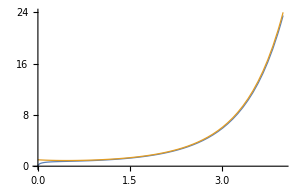

```mathematica
Plot[{stir[x],x!},{x,0,4},ImageSize->300,PlotStyle->Thickness[0.003]]
```

15.  Birthday problem. What is the probability that in a group of 20 people (that includes no twins) at least two have the same birthday, if we assume that the probability of having birthday on a given day is 1/365 for every day. First guess. Hint. Consider the complementary event.

I played with hypergeometric and discrete-uniform a little but could not get them to go. So I copied a pair of functions from MathWorld, and Eric Weisstein.

```mathematica
Clear["Global`*"]
```

```mathematica
prob[k_,n_,d_]:=1-Sum[qu[i,n,d],{i,k-1}]
qu[1,n_,d_]:=(d!)/((d-n)!d^n)
```

```mathematica
N[prob[2,20,365]]
```

0.411438

```mathematica
N[prob[2,30,365]]
```

0.706316

The following is not correct but I can’t help sticking it in just for the record.

```mathematica
d1=MultivariateHypergeometricDistribution[20,{346,19}];
```

```mathematica
r2=N[Probability[x≥0&&y≥2,{x,y}\[Distributed]d1]]
```

0.279476